```mathematica
Plot3D[Sin[2Pi t+b Sin[2Pi t]],{b,0,50},{t,0,1}
,ImageSize->Large
,BoxRatios->{2,2,1}
,PlotPoints->100
,Lighting->"Neutral"
,Mesh->{20}
,PlotRange->All]
```

-Graphics3D-

f_m mod. freq, a_m modulation intensity

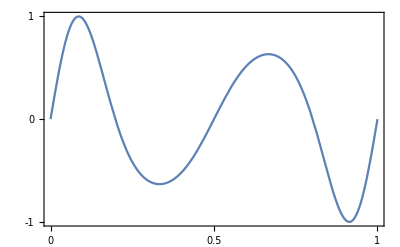
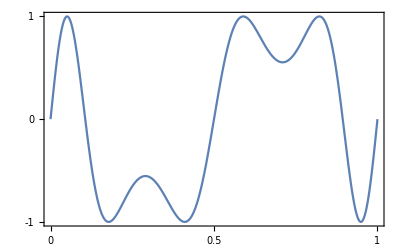
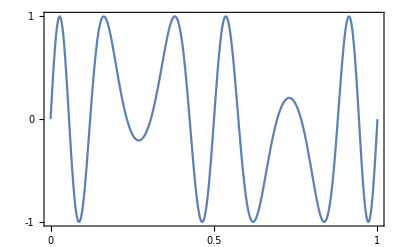
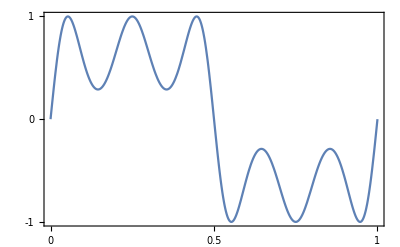
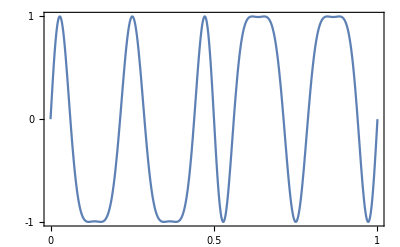
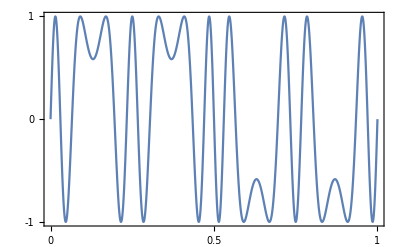
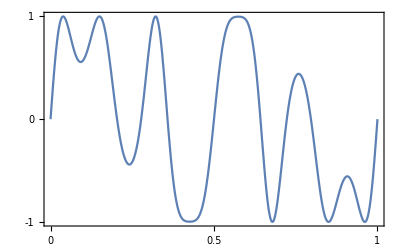
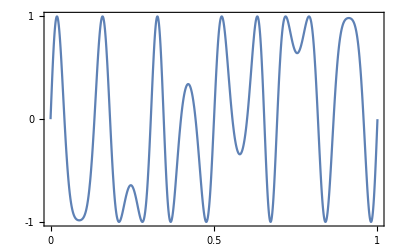
| a_m=1 | a_m=2 | a_m=4
f_m=1 | -Graphics- | -Graphics- | -Graphics-
f_m=2 | -Graphics- | -Graphics- | -Graphics-
f_m=3 | -Graphics- | -Graphics- | -Graphics-
f_m=4 | -Graphics- | -Graphics- | -Graphics-

```mathematica
ams={1,2,4};
fms={1,2,3,4};
ts=Partition[Flatten[Table[{Subscript[a, m],Subscript[f, m],Sin[2Pi t+2 Subscript[a, m] Sin[2 Subscript[f, m] Pi t]]},{Subscript[f, m],fms},{Subscript[a, m],ams}]],3];
fmPlots=Map[Plot[#[[3]],{t,0,1}
,PlotRange->Full
,Frame->True
,FrameTicks->{{{-1,0,1},None},{{0,.5,1},None}}
]&,ts];
TableForm[Partition[fmPlots,Length@ams]
,TableHeadings->{Table[StringJoin@{"f_m=",ToString@Subscript[f, m]},{Subscript[f, m],fms}]
,Table[StringJoin@{"a_m=",ToString@Subscript[a, m]},{Subscript[a, m],ams}]
}
,TableAlignments->Center
]
```